```mathematica
(* If the second argument of α or M is 0 that means it's appropriate for a dimension with Dirichlet boundary conditions, if it's 1, then that means it's appropriate for a dimension with Neumann boundary conditions *)
```

```mathematica
(* The α are related to the positions of the grid points *)
```

```mathematica
α[i_,0]:=BesselJZero[0,i]
α[i_,1]:=BesselJZero[1,i-1]
α[1,1]:=0
```

```mathematica
(* The M are related to the quasi-Gaussian quadrature weight (the weight is just 'r dr' or 'k dk' appropriately discretised) *)
```

```mathematica
M[i_,0]:=BesselJ[1,α[i,0]]^2
M[i_,1]:=BesselJ[0,α[i,1]]^2
```

```mathematica
(* 
If id=0,1 then we're transforming *to* a dimension with Dirichlet, Neumann boundary conditions respectively
If jd=0,1 then we're transforming *from* a dimension with Dirichlet, Neumann boundary conditions respectively
*)
```

```mathematica
T[Nmax_,id_,jd_,S_]:=2/S Table[1/M[j,jd] BesselJ[0,(α[i,id]α[j,jd])/S],{i,1,Nmax},{j,1,Nmax}]
```

```mathematica
T[2,0,0,S]
```

{{(2 BesselJ[0,BesselJZero[0,1]^2/S])/(S BesselJ[1,BesselJZero[0,1]]^2),(2 BesselJ[0,(BesselJZero[0,1] BesselJZero[0,2])/S])/(S BesselJ[1,BesselJZero[0,2]]^2)},{(2 BesselJ[0,(BesselJZero[0,1] BesselJZero[0,2])/S])/(S BesselJ[1,BesselJZero[0,1]]^2),(2 BesselJ[0,BesselJZero[0,2]^2/S])/(S BesselJ[1,BesselJZero[0,2]]^2)}}

```mathematica
FrobeniusNorm[matrix_]:=√Total[matrix^2,∞]
```

```mathematica
L2Norm[matrix_]:=√Max[Abs[Eigenvalues[Transpose[matrix].matrix]]]
```

```mathematica
L2Eigenvalues[matrix_]:=Eigenvalues[Transpose[matrix].matrix]
```

```mathematica
Error[matrix_]:=matrix-IdentityMatrix[Length[matrix]]
```

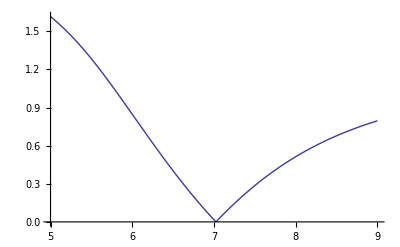

```mathematica
Plot[Evaluate[FrobeniusNorm[Error[T[2,0,1,S].T[2,1,0,S]]]],{S,5,9}]
```

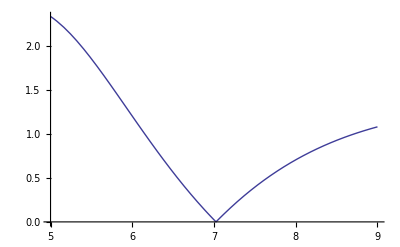

```mathematica
Plot[Evaluate[FrobeniusNorm[Error[T[2,1,0,S].T[2,0,1,S]]]],{S,5,9}]
```

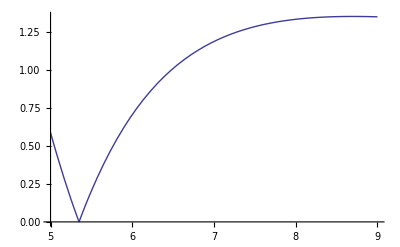

```mathematica
Plot[Evaluate[FrobeniusNorm[Error[T[2,1,1,S].T[2,1,1,S]]]],{S,5,9}]
```

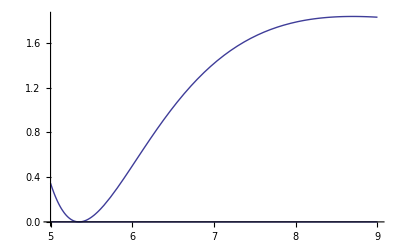

```mathematica
Plot[N[Evaluate[L2Eigenvalues[Error[T[2,1,1,S].T[2,1,1,S]]]],30],{S,5,9}]
```

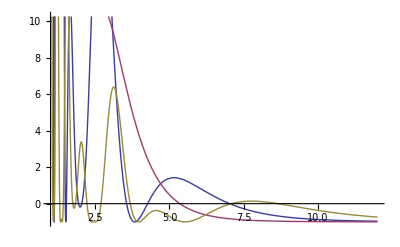

```mathematica
Plot[{Evaluate[Abs[Det[T[2,0,1,S].T[2,1,0,S]]]-1],Evaluate[Abs[Det[T[2,1,1,S].T[2,1,1,S]]]-1],Evaluate[Abs[Det[T[2,0,0,S].T[2,0,0,S]]]-1]},{S,1,12}]
```

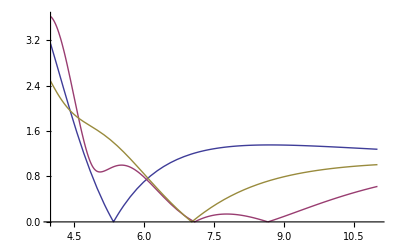

```mathematica
Plot[{N[Evaluate@L2Norm[Error[T[2,1,1,S].T[2,1,1,S]]],30],N[Evaluate@L2Norm[Error[T[2,0,0,S].T[2,0,0,S]]],30],N[Evaluate@L2Norm[Error[T[2,0,1,S].T[2,1,0,S]]],30]},{S,4,11}]
```

```mathematica
N[α[2,0]]
```

5.52008

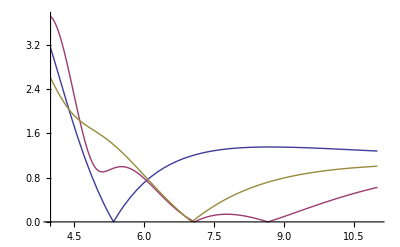

```mathematica
Plot[{N[Evaluate@FrobeniusNorm[Error[T[2,1,1,S].T[2,1,1,S]]],30],N[Evaluate@FrobeniusNorm[Error[T[2,0,0,S].T[2,0,0,S]]],30],N[Evaluate@FrobeniusNorm[Error[T[2,0,1,S].T[2,1,0,S]]],30]},{S,4,11}]
```

```mathematica
(* These functions can be used to compute the error for a given number of grid points.  "dd" means Dirichlet/Dirichlet boundary conditions; "dn" means Dirichlet/Neumann; and "nn" means Neumann/Neumann*)
```

```mathematica
TransformError[Nmax_,itype_,jtype_,S_?NumericQ]:=L2Norm[Error[T[Nmax,itype,jtype,S].T[Nmax,jtype,itype,S]]]
```

```mathematica
dd[Nmax_]:=FindMinValue[TransformError[Nmax,0,0,S],{S,α[Nmax+1,0]},WorkingPrecision->50]
```

```mathematica
dn[Nmax_]:=FindMinValue[TransformError[Nmax,0,1,S],{S,1/2(α[Nmax,0]+α[Nmax+1,0])},WorkingPrecision->50]
```

```mathematica
nn[Nmax_]:=FindMinValue[TransformError[Nmax,1,1,S],{S,1/2(α[Nmax,1]+α[Nmax+1,1])},WorkingPrecision->50]
```

```mathematica
{dd[5],dn[5],nn[5]}
```

FindMinValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than 50. digits of working precision to meet these tolerances.

{2.5819090701202877391634200270068288723339141480011×10^-7,0.00099563014242905563125702265462359587644335328083951,0.0022666435910963142604589106713570038299788778668083}

```mathematica
1/(2.5819090701202877391634200270068288723339141480010636353637450154385265`50.*^-7/0.00099563014242905563125702265462359587644335328083950600464959856740225612192`50.)
```

3856.178182071572860324445882997919698802938251057

```mathematica
Table[FindMinimum[Evaluate[FrobeniusNorm[Error[T[2,0,1,S].T[2,1,0,S]]]],{S,S0},WorkingPrecision->30],{S0,{3.5,4.5,7}}]
```

{{0.00140916203393541654265958912482,{S→7.02429341025245819361514816335}},{0.00140916203393541654265958912482,{S→-7.02429341025245819361514924442}},{0.00140916203393541654265958912482,{S→7.02429341025245819361514765345}}}

```mathematica
Table[FindMinimum[Evaluate[FrobeniusNorm[Error[T[2,0,0,S].T[2,0,0,S]]]],{S,S0},WorkingPrecision->30],{S0,{3.5,7,8.5}}]
```

{{2.01861240902364872941990815109,{S→3.3499272336689517871017486124}},{1.73123399465147524447134047676×10^-7,{S→8.65366486102125035353806802096}},{1.73123399465147524447134047676×10^-7,{S→8.65366486102125035353806801575}}}

```mathematica
Plot[{Evaluate@FrobeniusNorm[Error[T[2,0,1,S].T[2,1,0,S]]],Evaluate@FrobeniusNorm[Error[T[2,1,1,S].T[2,1,1,S]]],Evaluate@FrobeniusNorm[Error[T[2,0,0,S].T[2,0,0,S]]]},{S,4,9}]
```

$Aborted

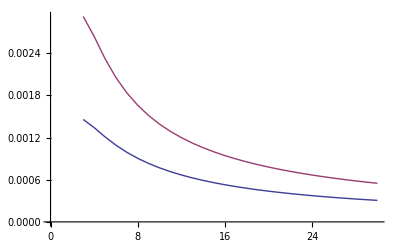

```mathematica
ListLinePlot[Table[Table[{Nmax,f[Nmax]},{Nmax,3,30}],{f,{dn,nn}}]]
```

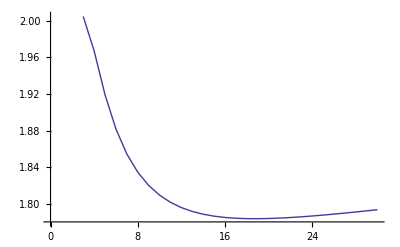

```mathematica
ListLinePlot[Table[{Nmax,nn[Nmax]/dn[Nmax]},{Nmax,3,30}]]
```

```mathematica
N[nn[50]/dn[50]]
```

1.81954

```mathematica
FindMinimum[Evaluate[FrobeniusNorm[Error[T[5,1,1,S].T[5,1,1,S]]]],{S,15},WorkingPrecision->30]
```

{0.0023225644830393213118347075378,{S→14.8668959607400875874055637748}}

```mathematica
FindRoot[Abs[Det[T[5,1,1,S]]]-1,{S,15},WorkingPrecision->30]
```

{S→14.8680449570494125700122934743}

```mathematica
N[T[5,1,1,14.8668959607400875874055637747886266670945196165641462421914`30.]-Inverse[T[5,1,1,14.8668959607400875874055637747886266670945196165641462421914`30.]]]//MatrixForm
```

(-0.000166501 | 0.0000698022 | -0.0000556464 | 0.0000398742 | 0.000125436
0.000430306 | -0.000180468 | 0.000144274 | -0.000106369 | -0.00028121
-0.000617816 | 0.000259837 | -0.000210231 | 0.000167404 | 0.000264639
0.000639496 | -0.000276727 | 0.000241819 | -0.000237332 | -0.0000361573
0.00263075 | -0.000956704 | 0.000499904 | -0.0000472831 | -0.000520458)

```mathematica
Det[T[5,1,1,14.8680449570494125700122934743017743657653536872661598412259`30.]]
```

1.

```mathematica
T[5,1,1,14.8680449570494125700122934743017743657653536872661598412259`30.].Inverse[T[5,1,1,14.8680449570494125700122934743017743657653536872661598412259`30.]]-IdentityMatrix[5]
```

{{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.}}

```mathematica
nn2[Nmax_]:=FindMinimum[Evaluate[FrobeniusNorm[Error[T[Nmax,1,1,S].T[Nmax,1,1,S]]]],{S,1/2(α[Nmax,1]+α[Nmax+1,1])},WorkingPrecision->30]
```

```mathematica
nn2[20]
```

{0.000780275655316258245012641120153,{S→62.0329403485773973471153830597}}

```mathematica
nn2[50]
```

{0.000349810532610481678155112838169,{S→156.28885212758170806420983382}}

```mathematica
Sopt50=156.2888521275817080642098338203934395240576009254824791774451`30.
```

156.28885212758170806420983382

```mathematica
Sopt=62.0329403485773973471153830597164190694599589910601949658491`30.;
```

```mathematica
rs[Nmax_,R_]:=Table[α[i,1]/(62.0329403485773973471153830597164190694599589910601949658491`30.)R,{i,1,Nmax}]
```

```mathematica
T[20,1,1,Sopt].Map[(1&),rs[20,1]]
```

{0.644818700761736837359721556243,1.169642362134291392834135864,1.06131149092366371115018667,1.16735726914087072276907309,1.17427316349801135681727067,1.25114221144636826030115577,1.28372540546923753836776855,1.35485174555930003264243487,1.40136652435963354896419685,1.47343518304022218982271149,1.53090943357754545775992498,1.60713489383833000874994081,1.67501515186601995511649783,1.75761174565678691172367004,1.83640304861191891505389587,1.9273421802127727115683353,2.01823724832204691305111595,2.11958963419886642855647094,2.22440950651269867934696056,2.33858232992517757858277051}

```mathematica
(1&)[3]
```

1

```mathematica
Map[(1&),rs[20,1]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
nn2[4]
```

{0.0026395862551407596516047182323,{S→11.7106474745937740215404188544}}

```mathematica
FindRoot[Evaluate[Abs[Det[T[20,1,1,S]]]-1],{S,62}]
```

$Aborted

```mathematica
N[BesselJZero[1,4]]
```

13.3237

```mathematica
T[4,1,1,11.7106474745937740215404188543629331136827127328838834429201`30.].{1,0,0,0}
```

{0.170784749890131689932891058127,0.170784749890131689932891058127,0.170784749890131689932891058127,0.170784749890131689932891058127}

```mathematica
Inverse[T[4,1,1,11.7106474745937740215404188543629331136827127328838834429201`30.]].{1,0,0,0}
```

{0.170498704435107621693558792,0.170903159386504857893784356,0.170707752826012849189724773,0.170595037855149116355122866}

```mathematica
Sopt
```

62.0329403485773973471153830597

```mathematica
N[α[2,1]]
```

3.83171

```mathematica
α[2,1]/Sopt
```

0.0617688916352549602256681037262

```mathematica
ks[Nmax_,R_]:=Table[α[i,1]/R,{i,1,Nmax}]
```

```mathematica
d=T[20,1,1,Sopt].(-(Inverse[T[20,1,1,Sopt]].Map[Cos[4#]Exp[-#^2]&,rs[20,8]])ks[20,8]ks[20,8])
```

{-35.69886068604582475198547,5.639461038275235620947538,4.574464643763331629380624,-3.987263760264102498856409,0.388168482293558175931821,0.292925414952322604282068,-0.051694868970243090091383,0.000972729793828635836552,-0.00491297386867266734707,0.005349428808964331105206,-0.004696690291913497989779,0.003979678132338065932233,-0.003294321699387757482442,0.002672797484157491878496,-0.0021215456985019258554,0.001635168655635758456583,-0.001203941269635330753733,0.0008168888447831889747298,-0.0004619805349004598406845,0.000116039946589791526195}

```mathematica
d2=T[20,1,1,Sopt].(-(Identity[T[20,1,1,Sopt]].Map[Cos[4#]Exp[-#^2]&,rs[20,8]])ks[20,8]ks[20,8]);
```

```mathematica
err[d_]:=d - Map[Limit[(4 ⅇ^(-r^2) (r (-5+r^2) Cos[4 r]+(-1+4 r^2) Sin[4 r]))/r,r->#]&,rs[20,8]]
```

```mathematica
err[d2]
```

{0.3006225268978838897706883,-0.1074553884549363211798474,0.0600725499434763576115389,-0.0309194177374081455437744,0.012526430187220315964722,-0.0019795530638528141898994,-0.00326430328379665656174566,0.00534355595728117277526489,-0.00575595685769417427887525,0.0053980375942718433382789,-0.00474457044159855528922391,0.00402258824370602408784668,-0.00332943986926879026134587,0.00269979539387260325718924,-0.0021399838595407191673702,0.0016445226286348175681781,-0.0012037154707656938495329,0.00080696886524421988316419,-0.0004441119354759096357675,0.00010581026405679270264338}

```mathematica
err[d]
```

{0.30113931395417524801453,-0.10766278841802848971922,0.060225783120384708114407,-0.031045169373584675678928,0.012634267739956731796985,-0.002074075957182682577643,-0.003180555277526148706966,0.005269084622724430659559,-0.005689867987564752549427,0.005339827385557720955994,-0.004694012274552894540953,0.00397966932589952693426,-0.003294323904529871595721,0.002672797496514755695725,-0.002121545698051263004657,0.00163516865563360393406,-0.001203941269635354005269,0.0008168888447831890560226,-0.0004619805349004598403795,0.000116039946589791526195}

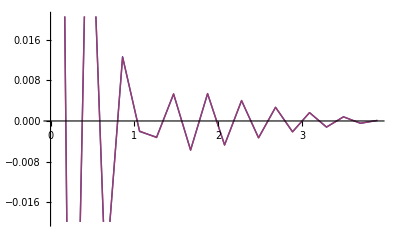

```mathematica
ListLinePlot[{Transpose[{rs[20,4],err[d]}],Transpose[{rs[20,4],err[d2]}]}]
```

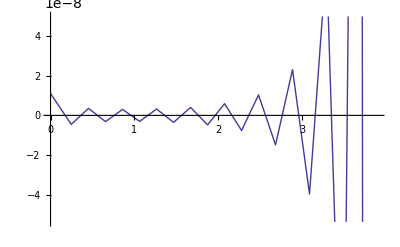

```mathematica
ListLinePlot[Transpose[{rs[20,4],err[d2]}]]
```

```mathematica
e2= d2 - Map[Limit[(Sin[r]-r (Cos[r]+r Sin[r]))/r^3,r->#]&,rs[20,10.90412165942889982714870279018868387209485885781872392257424189570009424049366`40.]]
```

{0.000442390008818705561207,-0.0001789721685344983117058,0.0001347718098021862863619,-0.0001140191435174619554647,0.0001020260167778285164547,-0.00009455223988223265532839,0.00008988011282652245570495,-0.00008719286967253946393229,0.00008607936051475589994544,-0.00008634740690152237156598,0.00008794580897216747451005,-0.00009093157872638162414593,0.00009545565814848227267319,-0.0001017430274121247367704,0.0001100068606729809329521,-0.000120070604523196396992,0.0001297153618268590982192,-0.0001268586499089087242863,0.00005038979837091401804518,-0.0001927898622701230735593}

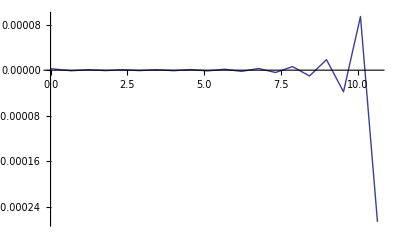

```mathematica
ListLinePlot[Transpose[{rs[20,10.90412165942889982714870279018868387209485885781872392257424189570009424049366`40.],e}],PlotRange->All]
```

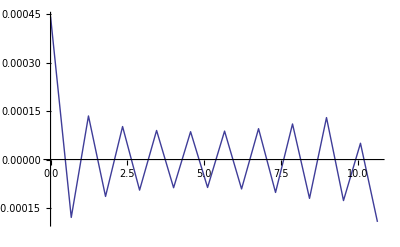

```mathematica
ListLinePlot[Transpose[{rs[20,10.90412165942889982714870279018868387209485885781872392257424189570009424049366`40.],e2}]]
```

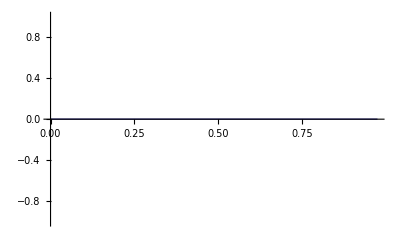

```mathematica
ListLinePlot[Transpose[{rs[20,1],e}]]
```

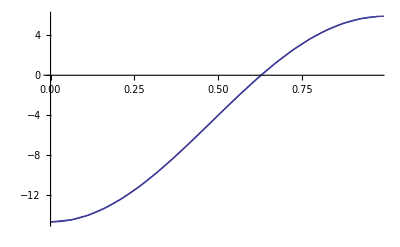

```mathematica
Show[ListLinePlot[Transpose[{rs[20,1],d}]],Plot[-α[2,1]^2 BesselJ[0,α[2,1]x],{x,0,1}]]
```

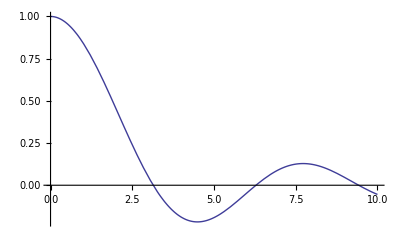

```mathematica
Plot[Sinc[x],{x,0,10}]
```

```mathematica
Reduce[Sinc'[x]==0,x]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Cos[x]/x-Sin[x]/x^2==0,x]

```mathematica
FindRoot[Sinc'[x],{x,10},WorkingPrecision->40]
```

{x→10.90412165942889982714870279018868387209}

```mathematica
rs[20,1]
```

{0,0.0617688916352549602256681037262,0.113094537037796683160993788206,0.164001062627301857761369320702,0.2147841430930941761195343544,0.26551425675335336733862347524,0.316216809976154755880177368435,0.366903200988033277470305163441,0.417579304512403820817513681101,0.468248455928350759892048504403,0.518912689453267391270043088985,0.569573316233979574906950662102,0.620231219390424360082084616506,0.670887015494645282180180296648,0.721541148076165441417737308512,0.772193944346601849819342325687,0.822845650983914578776489048442,0.873496457472113989672990094784,0.924146511768818709951524820974,0.974795931090089603289111887518}